```mathematica
raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2018-01-20]_IEEESE/Results/clean_data.csv"];
data=Import["/Users/thomaslux/Git/VarSys/Paper_[2018-01-20]_IEEESE/Results/IEEE_Main_Results.csv"];
sample=Import["/Users/thomaslux/Git/VarSys/Paper_[2018-01-20]_IEEESE/Results/Delaunay_Example_Prediction.csv"];
```

```mathematica
(* Functions for extracting rows from data based on values in certain columns *)
colNames=data[[1]]
algCol=Position[colNames,"Algorithm"][[1,1]];
tpCol=Position[colNames,"Training Percentage"][[1,1]];
ttCol=Position[colNames,"Test"][[1,1]];
ksCol=Position[colNames,"KS Statistic"][[1,1]];
testNames=Union[data[[All,ttCol]]][[1;;-2]];
algNames=Union[data[[All,algCol]]][[2;;-1]];
ksValues={0.1568,0.1879,0.2251,0.3110};
dataByVal[col_,vals_,d_:data]:={
select[row_]:=Length[Position[vals,row[[col]]]]>0;
Select[d,select]
}[[1]];
dataByTrainingPerc[p_:80,d_:data]:=dataByVal[tpCol,{p},d];
dataByAlg[alg_,d_:data]:=dataByVal[algCol,{alg},d];
dataByTest[test_,d_:data]:=dataByVal[ttCol,{test},d];
```

{Frequency,File Size,Record Size,Num Threads,Test,Algorithm,Training Percentage,Train Size,Test Size,Fit Time,Eval Time,KS Statistic,Average Absolute Error,Median Error,Average Error}

```mathematica
(* Generate the information for the table describing the unique values *)
For[i=1,i<8,i+=1,Print[colNames[[i]],"\t\t",Union[data[[All,i]]][[1;;-2]]]]
```

Frequency		{1200000,1600000,2000000,2300000,2800000,3200000,3500000}

File Size		{4,16,64,256,1024,4096,8192,16384}

Record Size		{4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384}

Num Threads		{1,8,16,24,32,40,48,56,64}

Test		{initial_writers,random_readers,random_writers,readers,re-readers,rewriters}

Algorithm		{Algorithm,Delaunay,MaxBoxMesh}

Training Percentage		{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95}

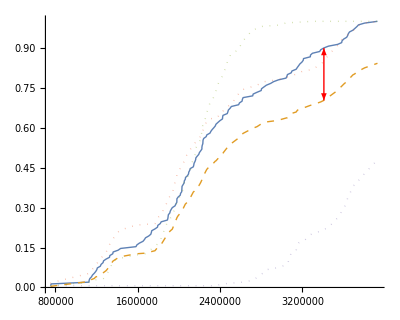

```mathematica
(* Generate Delaunay Example Prediction Plot *)
trueConfig=sample[[1,3;;6]];
trueValues=Sort[sample[[1,7;;-1]]];
trueDist=Interpolation[Transpose[{trueValues,CDF[EmpiricalDistribution[trueValues],trueValues]}],InterpolationOrder->1];
sourceConfigs={};
sourceDists={Transpose[{trueValues,trueDist[trueValues]}]};
AppendTo[sourceDists,Transpose[{trueValues,sample[[-1,7;;-1]]}]];
For[i=2,i≤Length[sample]-1,i+=1,{
AppendTo[sourceConfigs,sample[[i,3;;6]]];
sourceValues=sample[[i,7;;-1]];
minVal=Min[sourceValues];
maxVal=Max[sourceValues];
f=Interpolation[Transpose[{sourceValues,CDF[EmpiricalDistribution[sourceValues],sourceValues]}],InterpolationOrder->1];
AppendTo[sourceDists,Transpose[{trueValues,f[Clip[trueValues,{minVal,maxVal}]]}]];
}]
opac=0.5;
ratio=.8;
aSize=.03;
Show[ListLinePlot[sourceDists,LabelStyle->{FontFamily->"Times"},PlotStyle->{Thick,{Thick,Dashed},{Thick,Dotted,Opacity[opac]},{Thick,Dotted,Opacity[opac]},{Thick,Dotted,Opacity[opac]}},AspectRatio->ratio],Graphics[{Red,Thick,Arrowheads[{-aSize,aSize}],Arrow[{{3408768.28,0.70306},{3408768,0.89933}}]}]]
```

Raw data size:   {18376,150}

Min throughput:  1603.2

Max throughput:  3.84505×10^7

Num entries:     2756400

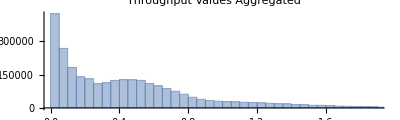

```mathematica
(* Generate the distributions of throughput for adding to the table and showing users the shape. *)
rawColNames=raw[[1]];
trialColStart=Position[rawColNames,"Trial 1"][[1,1]];
trialData=raw[[2;;-1,trialColStart;;-1]];
Print["Raw data size:   ",Dimensions[trialData]]
Print["Min throughput:  ",Min[trialData]]
Print["Max throughput:  ",Max[trialData]]
Print["Num entries:     ",Dimensions[Flatten[trialData]][[1]]]
ratio=0.3;
Histogram[{{},Flatten[trialData]},100,PlotLabel->"Throughput Values Aggregated",PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontFamily->"Times"}]
```

Shape of subdata: {16376}

Min and Max:      0.0274864  1

Shape of subdata: {16376}

Min and Max:      0.0319758  0.992771

Shape of subdata: {16376}

Min and Max:      0.0335245  0.999959

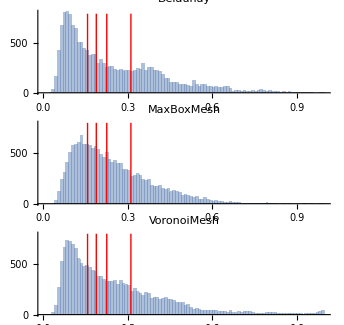

```mathematica
(* Distribution of performance by algorithm *)
(* KS Stats to P Values (for comparing two sets of 150 samples) *)
(*   0.1568      0.05    *)
(*   0.1879      0.01    *)
(*   0.2251      0.001   *)
(*   0.3110      1.0e-6  *)
plots={};
ratio=0.3;
For[i=1,i≤Length[algNames],i+=1,{
subdata=dataByAlg[algNames[[i]],dataByTrainingPerc[80]][[All,ksCol]];
Print["Shape of subdata: ",Dimensions[subdata]];
Print["Min and Max:      ",Min[subdata],"  ",Max[subdata]];
hist=Show[Histogram[{{},subdata},{0,1,1/100},PlotLabel->algNames[[i]],PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontFamily->"Times"}],
Graphics[{Red,Thick,Line[{{0.1568,0},{0.1568,800}}]}],
Graphics[{Red,Thick,Line[{{0.1879,0},{0.1879,800}}]}],
Graphics[{Red,Thick,Line[{{0.2251,0},{0.2251,800}}]}],
Graphics[{Red,Thick,Line[{{0.3110,0},{0.3110,800}}]}]];
AppendTo[plots,hist];
}]
GraphicsColumn[plots]
```

```mathematica
(* Data for table showing the prediction rates with the different varying p-values *)
For[i=1,i≤Length[algNames],i+=1,{
subdata=dataByAlg[algNames[[i]],dataByTrainingPerc[80]][[All,ksCol]];
Print["Algorithm: ",algNames[[i]]];
For[j=1,j≤Length[ksValues],j+=1,{
Print["  KS Stat: ",ksValues[[j]],", ",N[100*Count[subdata,ks_/;ks>ksValues[[j]]]/Length[subdata],3]];
}]
}]
```

Algorithm: Delaunay

KS Stat: 0.1568, 58.4

KS Stat: 0.1879, 51.1

KS Stat: 0.2251, 44.1

KS Stat: 0.311, 31.4

Algorithm: MaxBoxMesh

KS Stat: 0.1568, 69.3

KS Stat: 0.1879, 58.4

KS Stat: 0.2251, 46.9

KS Stat: 0.311, 26.6

Algorithm: VoronoiMesh

KS Stat: 0.1568, 61.9

KS Stat: 0.1879, 53.4

KS Stat: 0.2251, 45.1

KS Stat: 0.311, 28.7

```mathematica
(* Measuring the change in prediction performance with varying amounts of training data. *)
algNames=Union[data[[All,algCol]]][[2;;-1]]
ksVal=ksValues[[3]]
trainPercs=Union[data[[All,tpCol]]][[1;;-2]]
allScores={};
For[i=1,i≤Length[algNames],i+=1,{
subdata=dataByAlg[algNames[[i]]];
Print[algNames[[i]]];
algScores={};
For[j=1,j≤Length[trainPercs],j+=1,{
perf=dataByTrainingPerc[trainPercs[[j]],subdata][[All,ksCol]];
score=N[100*Count[perf,ks_/;ks>ksVal]/Length[perf],3];
AppendTo[algScores,{trainPercs[[j]],score}];
}];
AppendTo[allScores,algScores];
}];
```

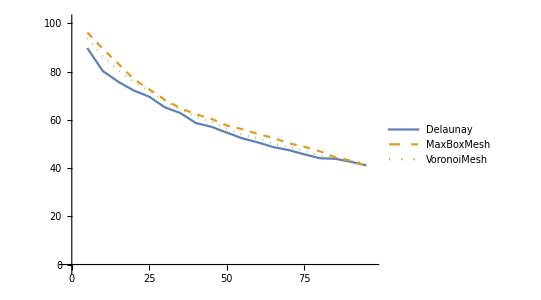

```mathematica
ratio=0.75;
Show[ListLinePlot[allScores,PlotStyle->{Medium,Dashed,Dotted},LabelStyle->{FontFamily->"Times"},AspectRatio->ratio,PlotLegends->Placed[algNames,{.3,.27}]]]
```

```mathematica
(* Measuring the change in prediction performance with varying amounts of training data per test *)
algNames=Union[data[[All,algCol]]][[2;;-1]]
ksVal=ksValues[[3]]
trainPercs=Union[data[[All,tpCol]]][[1;;-2]]
testPlots={};
For[t=1,t≤Length[testNames],t+=1,{
allScores={};
testdata=dataByTest[testNames[[t]]];
Print[testNames[[t]]];
For[i=1,i≤Length[algNames],i+=1,{
subdata=dataByAlg[algNames[[i]],testdata];
Print["  ",algNames[[i]]];
algScores={};
For[j=1,j≤Length[trainPercs],j+=1,{
perf=dataByTrainingPerc[trainPercs[[j]],subdata][[All,ksCol]];
score=N[100*Count[perf,ks_/;ks>ksVal]/Length[perf],3];
AppendTo[algScores,{trainPercs[[j]],score}];
}];
AppendTo[allScores,algScores];
}];
ratio=0.75;
p=ListLinePlot[allScores,PlotStyle->{Medium,Dashed,Dotted},LabelStyle->{FontFamily->"Times"},AspectRatio->ratio,PlotLabel->testNames[[t]],PlotRange->{0,100}];
AppendTo[testPlots,p];
}];
```

{Delaunay,MaxBoxMesh,VoronoiMesh}

0.2251

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95}

initial_writers

Delaunay

MaxBoxMesh

VoronoiMesh

random_readers

Delaunay

MaxBoxMesh

VoronoiMesh

random_writers

Delaunay

MaxBoxMesh

VoronoiMesh

readers

Delaunay

MaxBoxMesh

VoronoiMesh

re-readers

Delaunay

MaxBoxMesh

VoronoiMesh

rewriters

Delaunay

MaxBoxMesh

VoronoiMesh

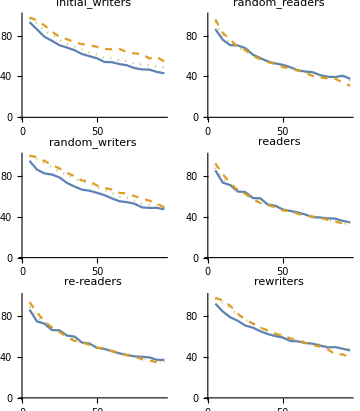

```mathematica
p=GraphicsGrid[{{testPlots[[1]],testPlots[[2]]},{testPlots[[3]],testPlots[[4]]},{testPlots[[5]],testPlots[[6]]}},ImageSize->Medium];
l=LineLegend[{Directive[ColorData[97,"ColorList"][[1]],Medium],Directive[ColorData[97,"ColorList"][[2]],Dashed],Directive[ColorData[97,"ColorList"][[3]],Dotted]},algNames,LegendLayout->"Row",LegendMarkerSize->20,LabelStyle->{FontFamily->"Times"}];
Export["/Users/thomaslux/Git/VarSys/Paper_[2018-01-20]_IEEESE/plot-KS-failure-by-training-and-test.pdf",Column[{l,p},Alignment->Center]];
Column[{l,p},Alignment->Center]
```